# Classical limit

```mathematica
Quit[]
```

## Resources

### IGraphM

```mathematica
(* Install Igraph the first time around, downloading it first from https://github.com/szhorvat/IGraphM/releases/download/v0.6.5/IGraphM-0.6.5.paclet *)
(*
Needs["PacletManager`"]
PacletInstall["~/Downloads/IGraphM-0.6.5.paclet"]
*)
```

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

Testing graph isomorphisms

```mathematica
ga=Graph[{1<->2,1<->2,2<->3}];
gb=Graph[{a<->b,a<->b,b<->c}];
```

```mathematica
(* Sadly built-in Mathematica Iso check sucks *)
IsomorphicGraphQ[ga,gb]
```

IsomorphicGraphQ::ngen: The generalized … is not implemented.

IsomorphicGraphQ[-Graphics-,-Graphics-]

```mathematica
(* But the one from IGraph does the job using edge colouring *)
IGVF2IsomorphicQ[IGColoredSimpleGraph[ga],IGColoredSimpleGraph[gb]]
```

True

### Signature assignment

```mathematica
ToUndirectedGraph[g_]:=Graph[Table[e/.{DirectedEdge[a_,b_,props__]:>UndirectedEdge[a,b,props]},{e,EdgeList[g]}]]
```

```mathematica
MakeAllExternalLegsIncoming[g_]:=Module[
{
OutgoingEdgesIndices
},
OutgoingEdgesIndices=Map[EdgeIndex[g,#⟦2⟧⟦1⟧]&,Select[Table[{iV,EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]]},{iV, VertexList[g]}],And[Length[#⟦2⟧]==1,EdgeCount[#⟦2⟧,DirectedEdge[_,#⟦1⟧,___]]==1]&]];
{OutgoingEdgesIndices,DirectedGraph[
Table[If[MemberQ[OutgoingEdgesIndices,ie],
EdgeList[g]⟦ie⟧/.{DirectedEdge[x_,y_,z___]:>DirectedEdge[y,x,z]},
EdgeList[g]⟦ie⟧
],{ie,Length[EdgeList[g]]}]
]}
]
```

```mathematica
cFFAssignSignaturesStartingFromEdge[g_Graph,startingVertex_,InputSignatures_]:=Module[{allIncomingEdges,allOutgoingEdges,otherVertexAndDirection,edgesWithoutSignature,signatures},signatures=Association[Table[k->InputSignatures[k],{k,Keys[InputSignatures]}]];
allIncomingEdges=EdgeList[g,DirectedEdge[_,startingVertex,_]];
allOutgoingEdges=EdgeList[g,DirectedEdge[startingVertex,_,_]];
edgesWithoutSignature=Select[Join[allIncomingEdges,allOutgoingEdges],Not[MemberQ[Keys[signatures],#]]&];
If[Length[edgesWithoutSignature]==1,Do[otherVertexAndDirection=e/.{DirectedEdge[startingVertex,a_,_]:>{a,1},DirectedEdge[a_,startingVertex,_]:>{a,-1}};
AssociateTo[signatures,e->(otherVertexAndDirection[[2]]*(Total[Table[signatures[eIN],{eIN,Select[allIncomingEdges,MemberQ[Keys[signatures],#]&]}]]-Total[Table[signatures[eOUT],{eOUT,Select[allOutgoingEdges,MemberQ[Keys[signatures],#]&]}]]))];
signatures=cFFAssignSignaturesStartingFromEdge[g,otherVertexAndDirection[[1]],signatures];,{e,edgesWithoutSignature}];];
signatures]
```

```mathematica
cFFGetEdgeSignatures[g_Graph,OptionsPattern[{lmb->Automatic,forceExternalVertices->Automatic}]]:=Module[{spanningTree,selectedLMB,leaves,startEdge,signatures,externalVertices,externalEdges,tmpA,leafEdge},
externalVertices=If[OptionValue[forceExternalVertices]===Automatic,
Sort[Select[VertexList[g],VertexDegree[g,#]===1&]],
OptionValue[forceExternalVertices]
];
If[OptionValue[lmb]===Automatic,
(*spanningTree=FindSpanningTree[ToUndirectedGraph[g]];*)
spanningTree=Select[EdgeList[g],MemberQ[
Table[e/.UndirectedEdge[_,_,props_]:>props["id"],{e,EdgeList[FindSpanningTree[ToUndirectedGraph[g]]]}],
GetEdgeProperty[#,"id"]]&];
selectedLMB=SortBy[Complement[EdgeList[g],EdgeList[spanningTree]],(#/.{DirectedEdge[a_,b_,name_]:>name})&];
,
spanningTree=DirectedGraph[Select[EdgeList[g],Not[MemberQ[OptionValue[lmb],(#/.{DirectedEdge[a_,b_,id_]:>id})]]&]];
selectedLMB=SortBy[Select[EdgeList[g],MemberQ[OptionValue[lmb],(#/.{DirectedEdge[a_,b_,id_]:>id})]&],Position[OptionValue[lmb],(#/.{DirectedEdge[a_,b_,id_]:>id})][[1]][[1]]&];
];
(*Assign signatures to externals now*)
signatures=Association[Table[tmpA=EdgeList[g,DirectedEdge[externalVertices[[iev]],_,_]];
(*It is much simpler if we force all externals incoming so check for this here*)If[Length[tmpA]!=1,Print["ERROR: please define all externals as incoming in your topology."];Return[Null];];
tmpA=If[Length[tmpA]==1,tmpA[[1]],EdgeList[g,DirectedEdge[_,externalVertices[[iev]],_]][[1]]];
tmpA->{Table[0,{i,Length[selectedLMB]}],Table[If[iev===j,1,0],{j,Length[externalVertices]}]},{iev,Length[externalVertices]}]];
(*And LMB edges now*)signatures=AssociateTo[signatures,Table[selectedLMB[[ie]]->{Table[If[ie===j,1,0],{j,Length[selectedLMB]}],Table[0,{i,Length[externalVertices]}]},{ie,Length[selectedLMB]}]];
(*And all others now*)leaves=Select[VertexList[spanningTree],VertexDegree[spanningTree,#]===1&];
leaves=Table[leafEdge=EdgeList[spanningTree,DirectedEdge[leaf,_,_]];
If[Length[leafEdge]==1,leafEdge=leafEdge[[1]];
If[MemberQ[Keys[signatures],leafEdge],leafEdge/.{DirectedEdge[_,x_,_]:>x},leaf],leafEdge=EdgeList[spanningTree,DirectedEdge[_,leaf,_]][[1]];
If[MemberQ[Keys[signatures],leafEdge],leafEdge/.{DirectedEdge[x_,_,_]:>x},leaf]],{leaf,leaves}];
Do[signatures=cFFAssignSignaturesStartingFromEdge[g,leaf,signatures];,{leaf,leaves}];
signatures]
```

```mathematica
AssignSignatures[INg_Graph,OptionsPattern[{lmb->Automatic,forceExternalVertices->Automatic}]]:=Module[
{g,signatures,flippedExternalEdgeIndices,flippedG,t,edge,externalFlips,signaturesFlipped},
t=MakeAllExternalLegsIncoming[INg];
flippedExternalEdgeIndices=t⟦1⟧;
flippedG=t⟦2⟧;
g=DirectedGraph[Table[EdgeList[flippedG][[ie]]/.{DirectedEdge[a_,b_]:>DirectedEdge[a,b,ie]},{ie,Length[EdgeList[flippedG]]}]];
signatures=cFFGetEdgeSignatures[g,lmb->OptionValue[lmb],forceExternalVertices->OptionValue[forceExternalVertices]];
externalFlips=Table[Position[signatures[EdgeList[g]⟦ie⟧]⟦2⟧,1]⟦1⟧⟦1⟧,{ie,flippedExternalEdgeIndices}];
signaturesFlipped=Association[Table[edge->{signatures[edge]⟦1⟧,Table[
If[MemberQ[externalFlips,is],-signatures[edge]⟦2⟧⟦is⟧,signatures[edge]⟦2⟧⟦is⟧]
,{is,Length[signatures[edge]⟦2⟧]}]},{edge,Keys[signatures]}]];
DirectedGraph[Table[
edge=EdgeList[g]⟦ie⟧;
edge/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[
If[MemberQ[flippedExternalEdgeIndices,ie],b,a],
If[MemberQ[flippedExternalEdgeIndices,ie],a,b],
Association[Join[
Table[p->props[p],{p,Keys[props]}],
{"sig"->If[MemberQ[flippedExternalEdgeIndices,ie],signatures[edge],signaturesFlipped[edge]]}
]]
]},{ie,Length[EdgeList[g]]}]]
]
```

```mathematica
ttt=-Graphics-;
```

```mathematica
MakeAllExternalLegsIncoming[ttt]
```

{{3,7},-Graphics-}

```mathematica
SortBy[Complement[EdgeList[ttt],EdgeList[spanningTree]],(#/.{DirectedEdge[a_,b_,name_]:>name})&];
```

Complement::heads: Heads EdgeList and List at positions 2 and 1 are expected to be the same.

Complement::heads: Heads List and EdgeList at positions 2 and 1 are expected to be the same.

```mathematica
ttt/
```

```mathematica
ToUndirectedGraph[ttt]
```

-Graphics-

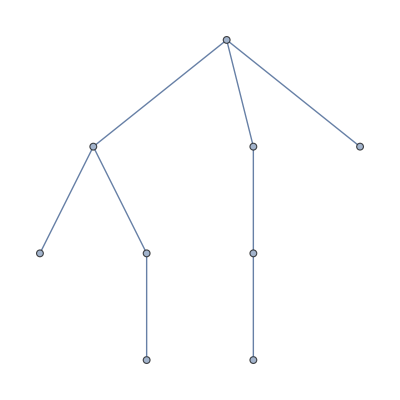

```mathematica
FindSpanningTree[ToUndirectedGraph[ttt]]
```

```mathematica
ttt
```

-Graphics-

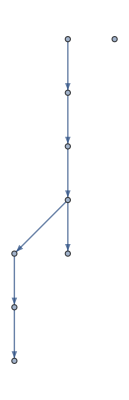

```mathematica
FindSpanningTree[ttt]
```

```mathematica
EdgeList[FindSpanningTree[]]
```

FindSpanningTree::argx: FindSpanningTree called with 0 arguments; 1 argument is expected.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[FindSpanningTree[]].

EdgeList[FindSpanningTree[]]

```mathematica
UndirectedGraph[ttt]
```

-Graphics-

```mathematica
EdgeList[FindSpanningTree[UndirectedGraph[ttt]]]
```

{{1,botIN}{3,bot}<|id→{1,botIN},sig→{{0,0,0,0,0},{1,0,0,0}}|>,{1,topIN}{3,top}<|id→{1,topIN},sig→{{0,0,0,0,0},{0,0,1,0}}|>,{3,bot}{4,bot}<|id→{3,bot},sig→{{-1,0,0,0,0},{1,0,0,0}}|>,{4,bot}{5,bot}<|id→{4,bot},sig→{{0,0,0,0,0},{1,0,0,0}}|>,{4,top}{2,topOUT}<|id→{2,topOUT},sig→{{0,0,0,1,0},{0,0,0,0}}|>,{5,bot}{2,botOUT}<|id→{2,botOUT},sig→{{0,0,1,0,0},{0,0,0,0}}|>,{3,top}<->{4,top},{3,top}<->{5,bot}}

```mathematica
Table[e/.UndirectedEdge[_,_,props_]:>props["id"],{e,EdgeList[FindSpanningTree[UndirectedGraph[ttt]]]}]
```

{{1,botIN},{1,topIN},{3,bot},{4,bot},{2,topOUT},{2,botOUT},{3,top}<->{4,top},{3,top}<->{5,bot}}

```mathematica
DirectedGraph[Select[EdgeList[ttt],MemberQ[
Table[e/.UndirectedEdge[_,_,props_]:>props["id"],{e,EdgeList[FindSpanningTree[ToUndirectedGraph[ttt]]]}],
GetEdgeProperty[#,"id"]]&]]
```

-Graphics-

```mathematica
AssignSignatures[ttt,forceExternalVertices->{{1,"botIN"},{2,"botOUT"},{1,"topIN"},{2,"topOUT"}}]
```

Part::partw: Part 1 of {} does not exist.

-Graphics-

### Graph Manipulation

```mathematica
GetEdgeProperty[edge_,prop_]:=(edge/.{DirectedEdge[_,_,props_]:>props})[prop]
```

```mathematica
ShowClassicalGraph[g_Graph,OptionsPattern[{Size->500,vLabels->Automatic,eLabels->Automatic,EdgeColours-><|1->Red,2->Darker[Green],3->Purple|>,Highlight->True}]]:=Module[{},

DirectedGraph[EdgeList[g],
ImageSize->OptionValue[Size],VertexLabels->OptionValue[vLabels],EdgeLabels->OptionValue[eLabels],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left},
EdgeStyle->If[OptionValue[Highlight],Join[
Table[
edge->OptionValue[EdgeColours][GetEdgeProperty[edge,"id"]⟦2⟧⟦2⟧]
,{edge,Select[EdgeList[g],And[ListQ[GetEdgeProperty[#,"id"]],ListQ[GetEdgeProperty[#,"id"]⟦2⟧],GetEdgeProperty[#,"id"]⟦2⟧⟦1⟧=="blob"]&]}
],
Table[
edge-> Directive[Blue,Thickness[0.002]]
,{edge,Select[EdgeList[g],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="top"]&]}
],
Table[
edge-> Directive[Darker[Darker[Blue]],Thickness[0.002]]
,{edge,Select[EdgeList[g],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="bot"]&]}
]
],Automatic],
VertexCoordinates->If[OptionValue[Highlight],{
{1,"topIN"}->{0,1},{2,"topOUT"}->{1,1},
{1,"botIN"}->{0,0},{2,"botOUT"}->{1,0}
},Automatic]
]
]
```

```mathematica
ShowClassicalGraphs[graphs_,OptionsPattern[{Ncolumns->3,Size->500,vLabels->Automatic,eLabels->None}]]:=Grid[Table[
Table[
Column[{Panel[Text[Style["Graph #"<>ToString[OptionValue[Ncolumns]i+ig+1],FontSize->13]],Alignment->Center,ImageSize->OptionValue[Size]],ShowClassicalGraph[graphs⟦OptionValue[Ncolumns]i+ig+1⟧,Size->OptionValue[Size],eLabels->OptionValue[eLabels],vLabels->OptionValue[vLabels]]}],
{ig,Range[0,Length[graphs⟦OptionValue[Ncolumns]i+1;;Min[OptionValue[Ncolumns](i+1),Length[graphs]]⟧]-1]}],{i,0,Floor[Length[graphs]/OptionValue[Ncolumns]]-1}]]
```

```mathematica
ConvertToSimpleGraph[g_]:=Module[{multiplicityMap,sortedVertices,newEdges},
multiplicityMap=<||>;
newEdges={};
Do[
sortedVertices=e/.{DirectedEdge[a_,b_,__]:>Sort[{a,b}]};
If[Not[MemberQ[Keys[multiplicityMap],sortedVertices]],
AssociateTo[multiplicityMap,sortedVertices->1];
AppendTo[newEdges,e];
,
AssociateTo[multiplicityMap,sortedVertices->multiplicityMap[sortedVertices]+1];
];
,{e,EdgeList[g]}
];
DirectedGraph[Table[
e/.{DirectedEdge[a_,b_,prop_]:>
DirectedEdge[a,b,
Association[Join[Table[k->prop[k],{k,Keys[prop]}],{"multiplicity"->multiplicityMap[Sort[{a,b}]]}]]
]
}
,{e,newEdges}]]
]
```

```mathematica
ColorGraph[g_,OptionsPattern[{taggedEdges->None,taggedVertices->None}]]:=Module[{coloredGraph,vColors,eColors,vTag,eTag},
coloredGraph=IGColoredSimpleGraph[UndirectedGraph[g]];
vColors=coloredGraph⟦2⟧⟦2⟧;
eColors=coloredGraph⟦3⟧⟦2⟧;
vTag=1000;
eTag=1000;
If[Not[OptionValue[taggedVertices]===None],
Do[If[MemberQ[OptionValue[taggedVertices],VertexList[g]⟦iv⟧],vColors⟦iv⟧=vColors⟦iv⟧+vTag;vTag+=1000;],{iv,Length[VertexList[g]]}];
];
If[Not[OptionValue[taggedEdges]===None],
Do[If[MemberQ[OptionValue[taggedEdges],GetEdgeProperty[EdgeList[g]⟦ie⟧,"id"]],eColors⟦ie⟧=eColors⟦ie⟧+eTag;eTag+=1000;],{ie,Length[EdgeList[g]]}];
];
{coloredGraph⟦1⟧,VertexColors->vColors,EdgeColors->eColors}
]
```

```mathematica
GenerateLoopGraphs[blobs_, OptionsPattern[{NtopVerticesRange->{1,2},NbotVerticesRange->{1,2},nLoops->2,tagExternal->True}]]:=Module[{
topMassiveLines, botMassiveLines, allGraphs, nIter, maxIter,
 allBlobCombinations,topTopo,botTopo,blobComb,externalVertices,newGraph, sewingMap,
iExternal,allColoredRepr, coloredRepr
},

(* Enumerat possible topologies of top and bot massive lines at 2-loop *)
topMassiveLines= Table[
DirectedGraph[
Join[{
DirectedEdge[{1,"topIN"},{3,"top"},<|"id"->{1,"topIN"}|>]
},
Table[
DirectedEdge[{iProp+2,"top"},{iProp+3,"top"},<|"id"->{iProp+2,"top"}|>],{iProp,1,nProp}],
{
DirectedEdge[{nProp+3,"top"},{2,"topOUT"},<|"id"->{2,"topOUT"}|>]
}
]
],
{nProp,OptionValue[NtopVerticesRange]⟦1⟧,OptionValue[NtopVerticesRange]⟦2⟧}];

botMassiveLines= Table[
DirectedGraph[
Join[{
DirectedEdge[{1,"botIN"},{3,"bot"},<|"id"->{1,"botIN"}|>]
},
Table[
DirectedEdge[{iProp+2,"bot"},{iProp+3,"bot"},<|"id"->{iProp+2,"bot"}|>],{iProp,1,nProp}],
{
DirectedEdge[{nProp+3,"bot"},{2,"botOUT"},<|"id"->{2,"botOUT"}|>]
}
]
],
{nProp,OptionValue[NbotVerticesRange]⟦1⟧,OptionValue[NbotVerticesRange]⟦2⟧}];

(* Now loop over all top line, bot lines and blob topologies, and generate graphs this way. Not the most efficient by far but it works *)

allGraphs={};
allColoredRepr={};
nIter=0;
allBlobCombinations=Join@@Table[
DeleteDuplicates[Table[Sort[c],{c,Tuples@Table[Range[Length[blobs]],{i,nBlobs}]}]],
{nBlobs,1,OptionValue[nLoops]+1}];

maxIter=Length[allBlobCombinations]Length[topMassiveLines]Length[botMassiveLines];
Monitor[
Do[
topTopo=topMassiveLines⟦iTopTopology⟧;
Do[
botTopo=botMassiveLines⟦iBotTopology⟧;
Do[
blobComb=Table[blobs[[iBlob]],{iBlob,allBlobCombinations⟦iBlobCombination⟧}];
nIter+=1;

(* First make sure there is the right number of vertices to glue *)
If[
(Length[VertexList[topTopo]]-2)+(Length[VertexList[botTopo]]-2)!=Total[Table[Length[blob["external_vertices"]],{blob,blobComb}]],
Continue[];
];
externalVertices=Join@@Table[Table[{vertex,iBlob},{vertex,blobComb⟦iBlob⟧["external_vertices"]}],{iBlob,1,Length[blobComb]}];

(* Now sew the vertices of the massive lines with the blob extrnal vertices in all possible ways *)
Do[
sewingMap=<||>;
iExternal=0;
Do[
iExternal+=1;
AssociateTo[sewingMap,sewingOrder⟦iExternal⟧->(topEdge/.{DirectedEdge[a_,b_,__]:>a})],
{topEdge,EdgeList[topTopo]⟦2;;⟧}
];
Do[
iExternal+=1;
AssociateTo[sewingMap,sewingOrder⟦iExternal⟧->(botEdge/.{DirectedEdge[a_,b_,__]:>a})],
{botEdge,EdgeList[botTopo]⟦2;;⟧}
];

newGraph=DirectedGraph[
Join[
EdgeList[topTopo],EdgeList[botTopo],
Join@@Table[Table[
edge/.{
DirectedEdge[a_,b_,__]:>
DirectedEdge[
If[MemberQ[Keys[sewingMap],{a,iBlob}],sewingMap[{a,iBlob}],{a,iBlob}],
If[MemberQ[Keys[sewingMap],{b,iBlob}],sewingMap[{b,iBlob}],{b,iBlob}],
<|"id"->{GetEdgeProperty[edge,"id"],{"blob",iBlob}}|>]
}
,{edge,EdgeList[blobComb⟦iBlob⟧["graph"]]}],{iBlob,1,Length[blobComb]}]
]
];

(* Immediately dismiss disconnected graphs *)
If[Not[WeaklyConnectedGraphQ[newGraph]],
Continue[];
];

(* Remove isomorphic copies *)
coloredRepr =If[OptionValue[tagExternal],
ColorGraph[newGraph,taggedVertices->{{1,"topIN"},{2,"topOUT"},{1,"botIN"},{2,"botOUT"}}],
ColorGraph[newGraph]
];

If[AnyTrue[allColoredRepr,IGVF2IsomorphicQ[coloredRepr,#]&],
Continue[];
];
AppendTo[allColoredRepr,coloredRepr];

newGraph=AssignSignatures[newGraph,forceExternalVertices->{{1,"botIN"},{2,"botOUT"},{1,"topIN"},{2,"topOUT"}}];
(*
Print[newGraph];
Pause[0.2];
*)
(* Filter lower loop graphs *)
If[Length[GetEdgeProperty[EdgeList[newGraph]⟦1⟧,"sig"]⟦1⟧]!=OptionValue[nLoops],
Continue[];
];

(* Only Keep 1PI *)
If[Length[Select[EdgeList[newGraph],AllTrue[GetEdgeProperty[#,"sig"]⟦1⟧,Function[sig,sig==0]]&]]!=4,
Continue[];
];

AppendTo[allGraphs,newGraph];

,{sewingOrder,Permutations[externalVertices]}];
,{iBlobCombination,Length[allBlobCombinations]}];
,{iBotTopology, Length[botMassiveLines]}];
,{iTopTopology, Length[topMassiveLines]}];
,
Row[{
("iTopTopo: "<>ToString[iTopTopology]<>"/"<>ToString[ Length[topMassiveLines]]<>" | "<>
"iBotTopo: "<>ToString[iBotTopology]<>"/"<>ToString[ Length[botMassiveLines]]<>" | "<>
"iBlobComb: "<>ToString[iBlobCombination]<>"/"<>ToString[ Length[allBlobCombinations]]<>" | "<>
"nGraphs: "<>ToString[Length[allGraphs]]<>" | "
),
ProgressIndicator[nIter,{0,maxIter}],
" | "<>ToString[nIter]<>"/"<>ToString[maxIter]<>" ("<>ToString[N[100*nIter/maxIter,3]]<>"%)"
}]
];

allGraphs
]
```

## 2-loop

Define the blob constituents

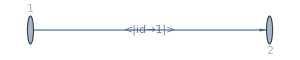
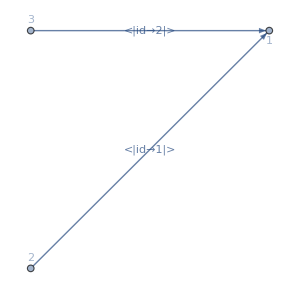

```mathematica
twoLoopsBlobs = {
<|
"id"->1,
"external_vertices"->{1,2},
"graph"->DirectedGraph[{
DirectedEdge[1,2,<|"id"->1|>]
}]
|>,
<|
"id"->2,
"external_vertices"->{1,2,3},
"graph"->DirectedGraph[{
DirectedEdge[2,1,<|"id"->1|>],
DirectedEdge[3,1,<|"id"->2|>]
}]
|>
};
Table[ShowClassicalGraph[b["graph"],Highlight->False,Size->300],{b,twoLoopsBlobs}]//Row
```

General all classical 2->2 graphs using them

```mathematica
TwoLoopClassicalGraphs=GenerateLoopGraphs[twoLoopsBlobs,tagExternal->True];
```

A total of 39 graphs were found

```mathematica
Length[TwoLoopClassicalGraphs]
```

39

Display the first one with all details

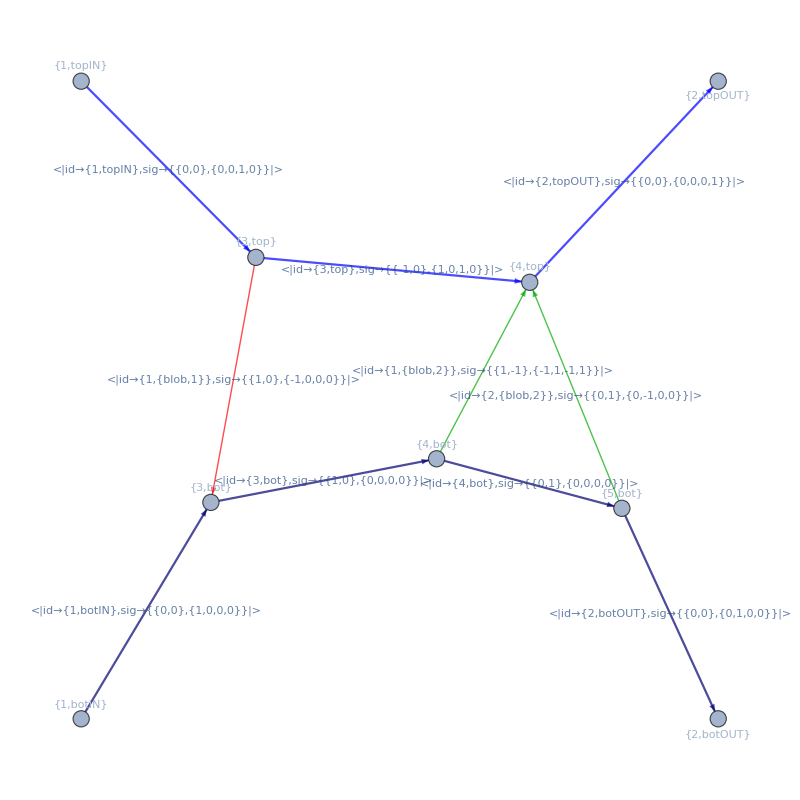

```mathematica
ShowClassicalGraph[TwoLoopClassicalGraphs⟦1⟧,Size->800,eLabels->Automatic]
```

Now display all 39 of them

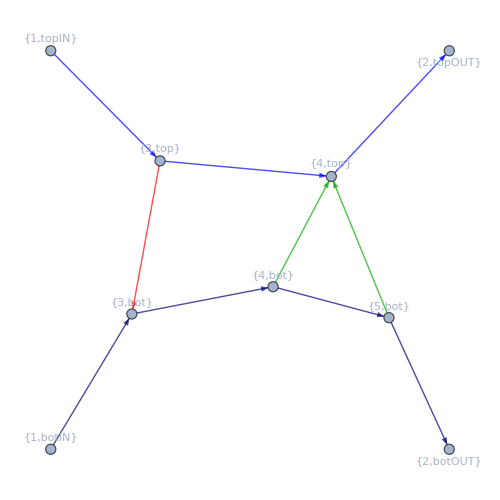
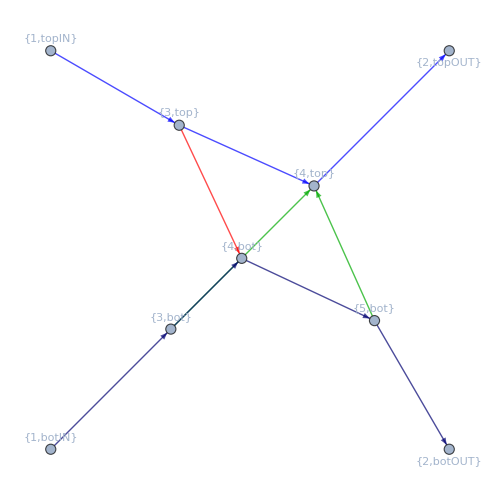
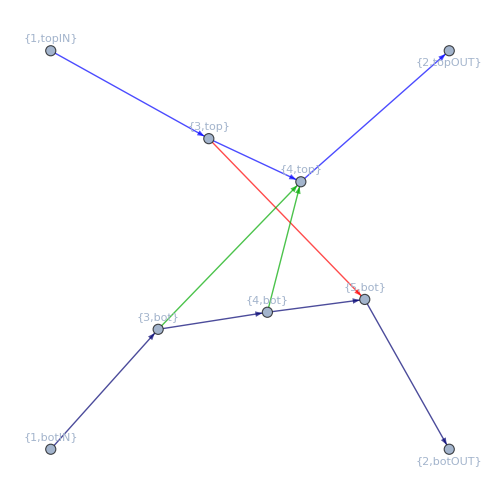
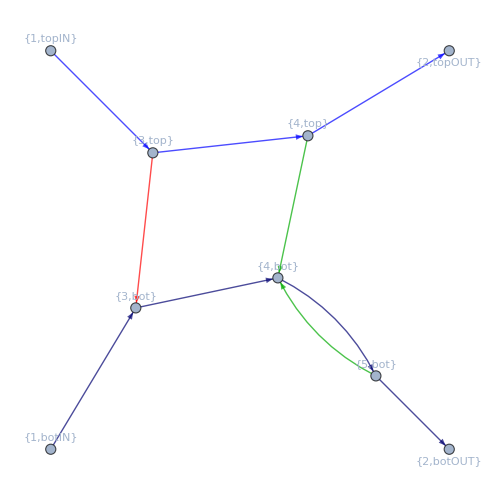
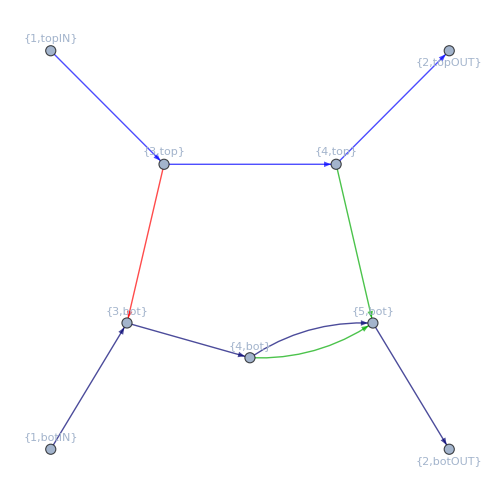
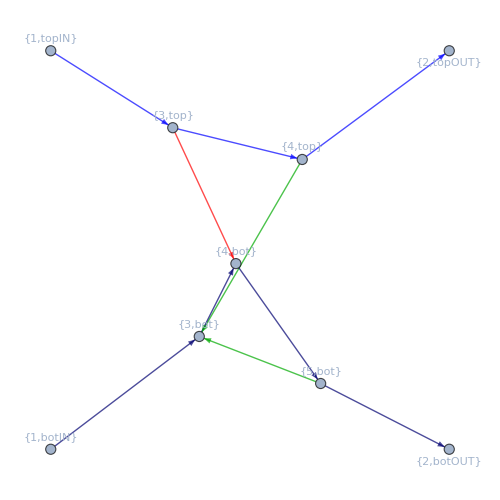
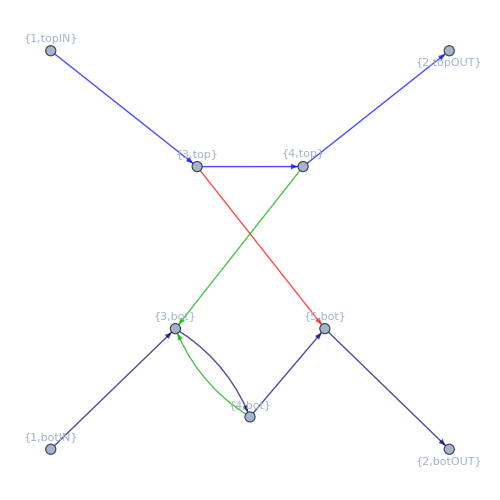
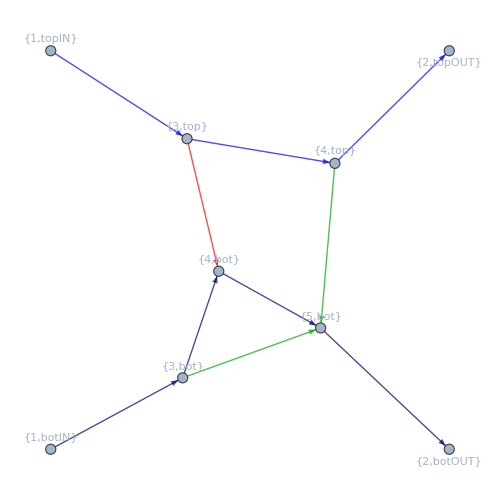
Graph #1
-Graphics- | Graph #2
-Graphics- | Graph #3
-Graphics-
Graph #4
-Graphics- | Graph #5
-Graphics- | Graph #6
-Graphics-
Graph #7
-Graphics- | Graph #8
-Graphics- | Graph #9
-Graphics-
Graph #10
-Graphics- | Graph #11
-Graphics- | Graph #12
-Graphics-
Graph #13
-Graphics- | Graph #14
-Graphics- | Graph #15
-Graphics-
Graph #16
-Graphics- | Graph #17
-Graphics- | Graph #18
-Graphics-
Graph #19
-Graphics- | Graph #20
-Graphics- | Graph #21
-Graphics-
Graph #22
-Graphics- | Graph #23
-Graphics- | Graph #24
-Graphics-
Graph #25
-Graphics- | Graph #26
-Graphics- | Graph #27
-Graphics-
Graph #28
-Graphics- | Graph #29
-Graphics- | Graph #30
-Graphics-
Graph #31
-Graphics- | Graph #32
-Graphics- | Graph #33
-Graphics-
Graph #34
-Graphics- | Graph #35
-Graphics- | Graph #36
-Graphics-
Graph #37
-Graphics- | Graph #38
-Graphics- | Graph #39
-Graphics-

```mathematica
ShowClassicalGraphs[TwoLoopClassicalGraphs,Size->500,Ncolumns->3,eLabels->None,vLabels->Automatic]
```